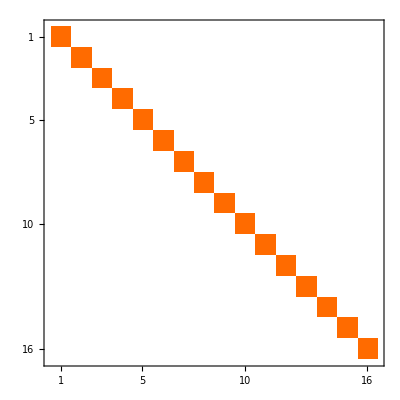

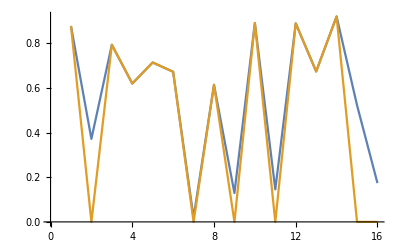

```mathematica
(* number of sampling points *) m=16;(* number of basis to be recovered *) rm=11 ;
(f = RandomReal[1,m]);
(basis = DiscreteHadamardTransform/@IdentityMatrix[m])//MatrixPlot;
(basis = IdentityMatrix[m])//MatrixPlot
R=f;
n=1;
a = Table[0, m];
γ= Table[0,m];
While[n<rm,
inner = Abs[basis.R];
{γ[[n]]} =FirstPosition[inner, Max[inner]];
a[[n]]=R.basis[[γ[[n]]]];
R=R - a[[n]]*basis[[γ[[n]]]];
n = n+1;
]
rf = Sum[a[[n]]*basis[[γ[[n]]]], {n,rm}];
ListLinePlot[{f,rf}]
```